```mathematica
(*Import packages*)
$LoadFeynArts = True;
$FeynCalcStartupMessages = False;
<< FeynCalc`
$FAVerbose = 0;
AppendTo[$Path, "C:\\Users\\Bruker\\Documents\\Skole\\master\\masteroppgave\\code\\mathematica\\include"];
<< XSec`
<< TreeLevel`
<< CalcTools`
```

Index::shdw: Symbol Index appears in multiple contexts {FeynCalc`,FeynArts`}; definitions in context FeynCalc` may shadow or be shadowed by other definitions.

IndexDelta::shdw: Symbol IndexDelta appears in multiple contexts {FeynCalc`,FeynArts`}; definitions in context FeynCalc` may shadow or be shadowed by other definitions.

CT::shdw: Symbol CT appears in multiple contexts {CalcTools`,Global`}; definitions in context CalcTools` may shadow or be shadowed by other definitions.

```mathematica
MakeBoxes[DSf[s_,t_,g_],TraditionalForm]:=SubscriptBox["Δ",MakeBoxes[s,TraditionalForm]]
MakeBoxes[DZ,TraditionalForm]=SubscriptBox["Δ","Z"];
MakeBoxes[Den[p2_,m2_],TraditionalForm]:=MakeBoxes[1/(p2-m2),TraditionalForm]
```

```mathematica
$Assumptions={s∈PositiveReals,t∈Reals,u∈Reals,L≠R}
```

{s∈ℝ∧s>0,t∈ℝ,u∈ℝ,L≠R}

```mathematica
Qt[a_,x_,y_]:=Den[s,DZ]Zs[x]*KroneckerDelta[x,y]-Den[t,DSf[a,3,1]] QtuC[a,x,y]*
QtC[a_,x_,y_]:=Den[s,DZ*]Zs[x]KroneckerDelta[x,y]-Den[t,DSf[a,3,1]*] QtuC[a,x,y]
Qu[a_,x_,y_]:=-Den[s,DZ]Zs[x]KroneckerDelta[x,y]+Den[u,DSf[a,3,1]] QtuC[a,y,x]
QuC[a_,x_,y_]:=-Den[s,DZ*]Zs[x]*KroneckerDelta[x,y]+Den[u,DSf[a,3,1]*] QtuC[a,y,x]*
```

```mathematica
Collect[(Qt[A,L,L]QuC[B,L,L]+Qu[B,L,L]QtC[A,L,L]+Qt[A,R,R]QuC[B,R,R]+Qu[B,R,R]QtC[A,R,R])//Expand//.{Conjugate[a_+b_]->a*+b*,Conjugate[a_*b_]->a**b*},Den[args1__]Den[args2__]]
Collect[-(Qt[A,L,R]QuC[B,L,R]+Qu[B,L,R]QtC[A,L,R]+Qt[A,R,L]QuC[B,R,L]+Qu[B,R,L]QtC[A,R,L])/.{KroneckerDelta[L,R]->0}//Expand//.{Conjugate[a_+b_]->a*+b*,Conjugate[a_*b_]->a**b*},Den[args1__]Den[args2__]]
Collect[(Qt[A,L,L]QtC[B,L,L]+Qt[A,L,R]QtC[B,L,R]+Qt[A,R,L]QtC[B,R,L]+Qt[A,R,R]QtC[B,R,R])/.{KroneckerDelta[L,R]->0}//Expand//.{Conjugate[a_+b_]->a*+b*,Conjugate[a_*b_]->a**b*},Den[args1__]Den[args2__]]
```

1/(t-Δ_A) 1/(u-Conjugate[(Δ_B)]) (-Conjugate[(Q_A^(L L̄))] Conjugate[(Q_B^(L L̄))]-Conjugate[(Q_A^(R R̄))] Conjugate[(Q_B^(R R̄))])+1/(u-Δ_B) 1/(t-Conjugate[(Δ_A)]) (-Q_A^(L L̄) Q_B^(L L̄)-Q_A^(R R̄) Q_B^(R R̄))+1/(t-Δ_A) 1/(s-Conjugate[(Δ_Z)]) (Conjugate[(Z_s^L)] Conjugate[(Q_A^(L L̄))]+Conjugate[(Z_s^R)] Conjugate[(Q_A^(R R̄))])+1/(s-Δ_Z) 1/(t-Conjugate[(Δ_A)]) (Z_s^L Q_A^(L L̄)+Z_s^R Q_A^(R R̄))+1/(s-Δ_Z) 1/(u-Conjugate[(Δ_B)]) (Conjugate[(Z_s^L)] Conjugate[(Q_B^(L L̄))]+Conjugate[(Z_s^R)] Conjugate[(Q_B^(R R̄))])+1/(u-Δ_B) 1/(s-Conjugate[(Δ_Z)]) (Z_s^L Q_B^(L L̄)+Z_s^R Q_B^(R R̄))+1/(s-Δ_Z) 1/(s-Conjugate[(Δ_Z)]) (-(Conjugate[(Z_s^L)])^2-(Conjugate[(Z_s^R)])^2-(Z_s^L)^2-(Z_s^R)^2)

1/(t-Δ_A) 1/(u-Conjugate[(Δ_B)]) (Conjugate[(Q_A^(R L̄))] Conjugate[(Q_B^(L R̄))]+Conjugate[(Q_A^(L R̄))] Conjugate[(Q_B^(R L̄))])+1/(u-Δ_B) 1/(t-Conjugate[(Δ_A)]) (Q_A^(R L̄) Q_B^(L R̄)+Q_A^(L R̄) Q_B^(R L̄))

1/(t-Δ_A) 1/(t-Conjugate[(Δ_B)]) (Q_B^(L R̄) Conjugate[(Q_A^(L R̄))]+Q_B^(R L̄) Conjugate[(Q_A^(R L̄))]+Q_B^(L L̄) Conjugate[(Q_A^(L L̄))]+Q_B^(R R̄) Conjugate[(Q_A^(R R̄))])+1/(t-Δ_A) 1/(s-Conjugate[(Δ_Z)]) (Z_s^L (-Conjugate[(Q_A^(L L̄))])-Z_s^R Conjugate[(Q_A^(R R̄))])+1/(s-Δ_Z) 1/(t-Conjugate[(Δ_B)]) (Q_B^(L L̄) (-Conjugate[(Z_s^L)])-Q_B^(R R̄) Conjugate[(Z_s^R)])+1/(s-Δ_Z) 1/(s-Conjugate[(Δ_Z)]) (Z_s^L Conjugate[(Z_s^L)]+Z_s^R Conjugate[(Z_s^R)])

```mathematica
ReleaseSuperCharges={
QtuC[a_,x_,y_]->Csq[i,a,x]Csq[j,a,y]*,
Conjugate[a_*b_]->a*b*
};
```

```mathematica
QtuC[A,L,L]QtuC[B,L,L]/.ReleaseSuperCharges
QtuC[A,L,L]*QtuC[B,L,L]*/.ReleaseSuperCharges
QtuC[A,L,R]QtuC[B,R,L]*/.ReleaseSuperCharges
QtuC[A,L,R]*QtuC[B,R,L]*/.ReleaseSuperCharges
```

C_(q(q̃)_A(χ̃)_i^0)^L C_(q(q̃)_B(χ̃)_i^0)^L Conjugate[(C_(q(q̃)_A(χ̃)_j^0)^L)] Conjugate[(C_(q(q̃)_B(χ̃)_j^0)^L)]

C_(q(q̃)_A(χ̃)_j^0)^L C_(q(q̃)_B(χ̃)_j^0)^L Conjugate[(C_(q(q̃)_A(χ̃)_i^0)^L)] Conjugate[(C_(q(q̃)_B(χ̃)_i^0)^L)]

C_(q(q̃)_A(χ̃)_i^0)^L C_(q(q̃)_B(χ̃)_j^0)^L Conjugate[(C_(q(q̃)_A(χ̃)_j^0)^R)] Conjugate[(C_(q(q̃)_B(χ̃)_i^0)^R)]

C_(q(q̃)_A(χ̃)_j^0)^R C_(q(q̃)_B(χ̃)_j^0)^L Conjugate[(C_(q(q̃)_A(χ̃)_i^0)^L)] Conjugate[(C_(q(q̃)_B(χ̃)_i^0)^R)]

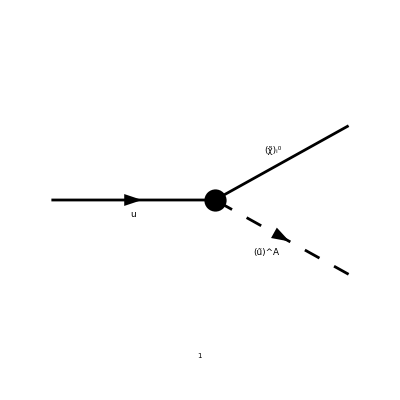

-Graphics-

```mathematica
ForwardRule = InsertFields[
CreateTopologies[0, 1->2], 
{F[3, {1,a}]} -> {F[11, {i}], S[13,{A,1,a}]},
 InsertionLevel -> {Classes},
 Model -> MSSMQCD];
Paint[ForwardRule, Numbering->Simple, ImageSize->{512,256}];
BackwardRule = InsertFields[
CreateTopologies[0, 1->2], 
{-F[3, {1,a}]} -> {F[11, {i}], -S[13,{A,1,a}]},
 InsertionLevel -> {Classes},
 Model -> MSSMQCD
];
Paint[ForwardRule, Numbering->Simple, ImageSize->{512,256}];
(*ForwardRule = InsertFields[
CreateTopologies[0, 2->1], 
{F[3, {1,a}],F[11, {i}] } -> {S[13,{A,1,a}]},
 InsertionLevel -> {Classes},
 Model -> MSSMQCD
];
Paint[ForwardRule, Numbering->Simple, ImageSize->{512,256}];
BackwardRule = InsertFields[
CreateTopologies[0, 2->1], 
{-F[3, {1,a}],F[11, {i}] } -> {-S[13,{A,1,a}]},
 InsertionLevel -> {Classes},
 Model -> MSSMQCD
];
Paint[BackwardRule, Numbering->Simple, ImageSize->{512,256}];*)
```

```mathematica
ForwardAmp=FCFAConvert[
CreateFeynAmp[ForwardRule,Truncated->True], 
IncomingMomenta->{p1,pA}, OutgoingMomenta->{pi,pA},
ChangeDimension->D,
UndoChiralSplittings->True,
List->False,
SMP->True,
DropSumOver->True,
LorentzIndexNames->{μ,ν}
]/.AmpSimplifyRules
BackwardAmp=FCFAConvert[
CreateFeynAmp[BackwardRule,Truncated->True], 
IncomingMomenta->{p1,pA}, OutgoingMomenta->{pi,pA},
ChangeDimension->D,
UndoChiralSplittings->True,
List->False,
SMP->True,
DropSumOver->True,
LorentzIndexNames->{μ,ν}
]/.AmpSimplifyRules
```

-ⅈ ((2 ⅈ √2 (γ̄)^6 g_W N_(i,1) (sin(θ_W)) (Q̃)_(A,2))/(3 (cos(θ_W)))-(ⅈ (γ̄)^7 g_W (3 m_W s_β (cos(θ_W)) (Q̃)_(A,1) Conjugate[(N_(i,2))]+m_W s_β (sin(θ_W)) (Q̃)_(A,1) Conjugate[(N_(i,1))]))/(3 √2 m_W s_β (cos(θ_W))))

ⅈ ((2 ⅈ √2 (γ̄)^7 g_W (sin(θ_W)) Conjugate[(N_(i,1))] Conjugate[((Q̃)_(A,2))])/(3 (cos(θ_W)))-(ⅈ (γ̄)^6 g_W Conjugate[((Q̃)_(A,1))] (3 N_(i,2) (cos(θ_W))+N_(i,1) (sin(θ_W))))/(3 √2 (cos(θ_W))))

```mathematica
MakeBoxes[Csq[a_,i_,x_],TraditionalForm]:=SubsuperscriptBox["C",RowBox[{SubsuperscriptBox[OverscriptBox["χ","~"],ToString[i],"0"],SubscriptBox[OverscriptBox["q","~"],ToString[a]],"q"}],ToString[x]]
CarlCharges={
USf[args__][a_,1]*ZNeu[i_,1]->(Csq[a,i,L]-1/2 USf[args][a,1]*ZNeu[i,2])/(SMP["sin_W"]/(6SMP["cos_W"])),
USf[args__][a_,1]ZNeu[i_,1]*->(Csq[a,i,L]*-1/2 USf[args][a,1]ZNeu[i,2]*)/(SMP["sin_W"]/(6SMP["cos_W"])),
USf[args__][a_,2]ZNeu[i_,1]->Csq[a,i,R]/(-(2SMP["sin_W"])/(3SMP["cos_W"])),
USf[args__][a_,2]*ZNeu[i_,1]*->Csq[a,i,R]*/(-(2SMP["sin_W"])/(3SMP["cos_W"]))
};
Convert2Carl[expr_]:=Collect[
expr,
{USf[args1__][args2__]ZNeu[args3__],USf[args1__][args2__]*ZNeu[args3__],USf[args1__][args2__]ZNeu[args3__]*,USf[args1__][args2__]*ZNeu[args3__]*},
Simplify
]/.CarlCharges//Simplify
```

```mathematica
MakeBoxes[Lsq[a_,i_],TraditionalForm]:=SubscriptBox["L",RowBox[{"q",SubscriptBox[OverscriptBox["q","~"],ToString[a]],SubsuperscriptBox[OverscriptBox["χ","~"],ToString[i],"0"]}]]
MakeBoxes[Rsq[a_,i_],TraditionalForm]:=SubscriptBox["R",RowBox[{"q",SubscriptBox[OverscriptBox["q","~"],ToString[a]],SubsuperscriptBox[OverscriptBox["χ","~"],ToString[i],"0"]}]]
DeboveCharges={
USf[args__][a_,2]ZNeu[i_,1]->Rsq[a,i]*/(-(2/3 SMP["sin_W"])/(√2 SMP["cos_W"])),
USf[args__][a_,2]*ZNeu[i_,1]*->Rsq[a,i]/(-(2/3 SMP["sin_W"])/(√2 SMP["cos_W"])),
USf[args__][a_,1]ZNeu[i_,1]*->(Lsq[a,i]*-(1/2 SMP["cos_W"]
ZNeu[i,2]*)/(√2 SMP["cos_W"])USf[args][a,1])/((1/6 SMP["sin_W"])/(√2 SMP["cos_W"])),
USf[args__][a_,1]*ZNeu[i_,1]->(Lsq[a,i]-(1/2 SMP["cos_W"]
ZNeu[i,2])/(√2 SMP["cos_W"])USf[args][a,1]*)/((1/6 SMP["sin_W"])/(√2 SMP["cos_W"]))
};
ReleaseDeboveCharges={
((Lsq[a_,i_]->(1/6 SMP["sin_W"]ZNeu[i_,1]+1/2 SMP["cos_W"]
ZNeu[i,2]))/(√2 SMP["cos_W"]))USf[3,1][a,1]*,
Rsq[a_,i_]->-((2/3 SMP["sin_W"]ZNeu[i,1]*)/(√2 SMP["cos_W"]))USf[3,1][a,2]*
};
Convert2Debove[expr_]:=Collect[
expr,
{USf[args1__][args2__]ZNeu[args3__],USf[args1__][args2__]*ZNeu[args3__],USf[args1__][args2__]ZNeu[args3__]*,USf[args1__][args2__]*ZNeu[args3__]*},
Simplify
]/.DeboveCharges//Simplify
```

```mathematica
Convert2Debove[ForwardAmp//Expand]
Convert2Debove[BackwardAmp//Expand]
Convert2Carl[ForwardAmp//Expand]
Convert2Carl[BackwardAmp//Expand]
```

-2 g_W ((γ̄)^7 Conjugate[(L_(q(q̃)_A(χ̃)_i^0))]+(γ̄)^6 Conjugate[(R_(q(q̃)_A(χ̃)_i^0))])

2 g_W ((γ̄)^6 L_(q(q̃)_A(χ̃)_i^0)+(γ̄)^7 R_(q(q̃)_A(χ̃)_i^0))

-√2 g_W ((γ̄)^7 C_((χ̃)_i^0(q̃)_A q)^L+(γ̄)^6 C_((χ̃)_i^0(q̃)_A q)^R)

√2 g_W ((γ̄)^6 Conjugate[(C_((χ̃)_i^0(q̃)_A q)^L)]+(γ̄)^7 Conjugate[(C_((χ̃)_i^0(q̃)_A q)^R)])

```mathematica
-√2 SMP["g_W"]Collect[%%/(-√2 SMP["g_W"]),DiracGamma[arg_],FullSimplify]
```

-√2 g_W ((γ̄)^7 C_((χ̃)_i^0(q̃)_A q)^L+(γ̄)^6 C_((χ̃)_i^0(q̃)_A q)^R)